```mathematica
(* Broadband pulses with fixed profile bandwidths ϵ = 0.2, 0.3, 0.4, ... *)
(* Minimized total pulse area ≤ 5π *)
(* Target probability: p = 1, 1/2, 1/4 *)
(* Error < 10^-3 *)
```

```mathematica
plotUtils=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"plot_utils.m"}];
<<(plotUtils)
```

```mathematica
root=rootBB;
err=0.001;
error=", error="<>ToString@err;
totalArea[rule_,npulses_]:=Module[{vars=rule/.Rule[a_,b_]->a},npulses Abs[vars[[-1]]/.rule]];
```

BB3; 1/2, 1/4, error=0.001

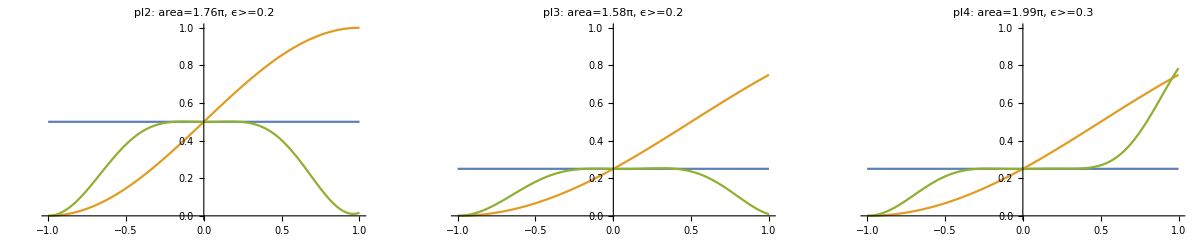

```mathematica
(*N=3 - could not find 1*)
sequence=U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,3]]

pl2=pltN[1/2,{Δ1->0.2454,Δ2->0.1084,Δ3->1.0135,Ω1->0.5868},"pl2"];
pl3=pltN[1/4,{Δ1->0.5014,Δ2->0.1567,Δ3->1.0419,Ω1->0.528},"pl3"];
pl4=pltN[1/4,{Δ1->0.9168,Δ2->-0.7971,Δ3->-0.6435,Ω1->0.6618},"pl4"];

GGrid[Text[Style["BB3; 1/2, 1/4"<> error,FontSize->20]],{{pl2,pl3,pl4}},ImageSize->Full]
```

```mathematica
(*N=4, 5 DO NOT OFFER SMALLER PULSE AREAS THAN N=3 - however larger bandwidhts can be obtained*)
```

BB4; p=1, error=0.001

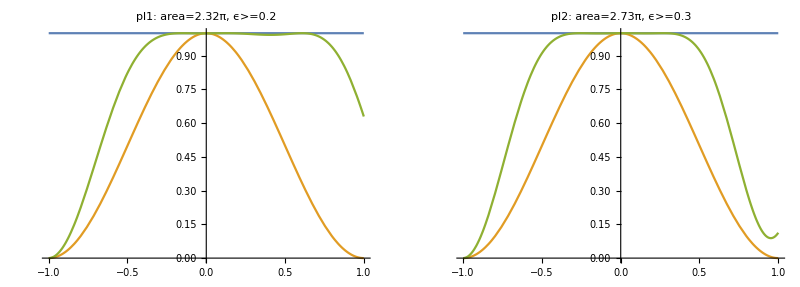

BB4; p=1/2, error=0.001

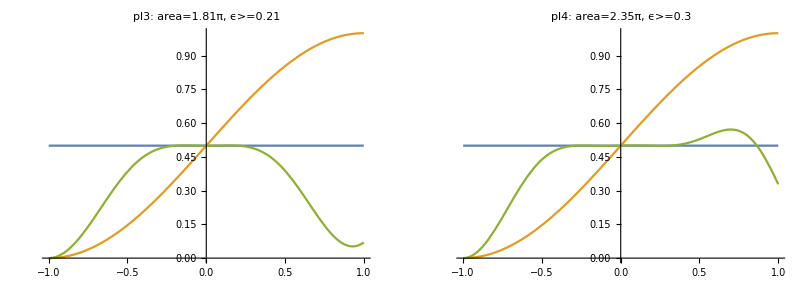

BB4; p=1/4, error=0.001

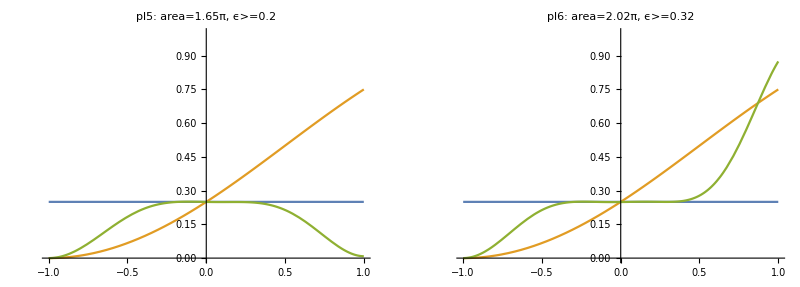

```mathematica
(*N=4 - BB3 provides smaller area, but BB4 provides BW=0.3*)
(*Choose this*)
sequence=U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,  totalArea[rule,4]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label,  totalArea[rule,4]]

pl1=pltS[1,{Δ1->-0.8659,Δ2->0.0032,Ω1->0.5806},"pl1"];
pl2=pltS[1,{Δ1->0.0206,Δ2->-0.8978,Ω1->0.6826},"pl2"];

pl3=pltN[1/2,{Δ1->0.8829,Δ2->0.2969,Δ3->0.0586,Δ4->0.2205,Ω1->0.4517},"pl3"];
pl4=pltN[1/2,{Δ1->0.5483,Δ2->0.0459,Δ3->-1.0613,Δ4->0.5013,Ω1->0.587},"pl4"];

pl5=pltN[1/4,{Δ1->0.4383,Δ2->0.1501,Δ3->0.3161,Δ4->0.9226,Ω1->0.4127},"pl5"];
pl6=pltN[1/4,{Δ1->1.0634,Δ2->0.2043,Δ3->0.3930,Δ4->0.1557,Ω1->0.5060},"pl6"];

GGrid[Text[Style["BB4; p=1"<> error,FontSize->20]],{{pl1,pl2,Null}},ImageSize->Full]
GGrid[Text[Style["BB4; p=1/2"<> error,FontSize->20]],{{pl3,pl4,Null}},ImageSize->Full]
GGrid[Text[Style["BB4; p=1/4"<> error,FontSize->20]],{{pl5,pl6,Null}},ImageSize->Full]
```

BB5 p=1, error=0.001

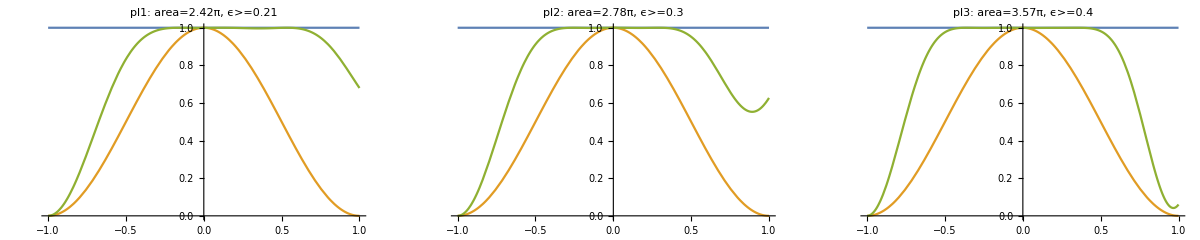

BB5 p=1/2, error=0.001

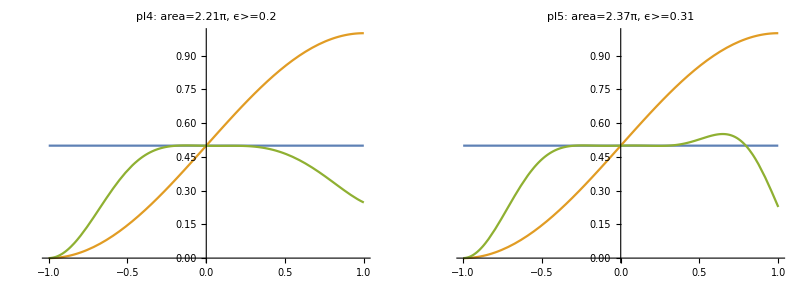

BB5 p=1/4, error=0.001

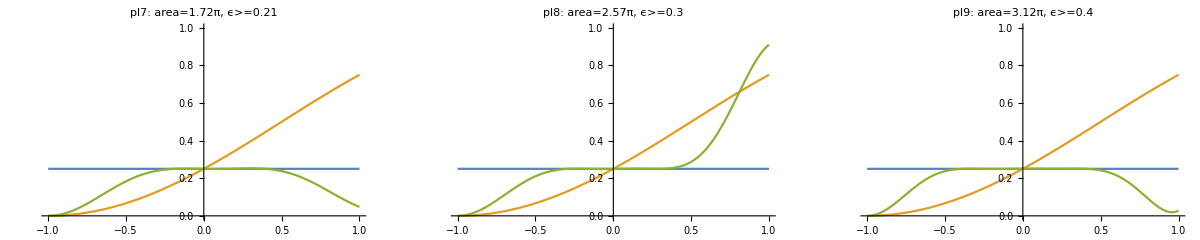

```mathematica
(*N=5 - BB4 provides smaller area, but BB5 provides BW=0.4 Couldn't not find 1/2 for 0.4*)
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[0,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequence=U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,  totalArea[rule,5]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label,  totalArea[rule,5]]

pl1=pltS[1,{Δ1->0.8330,Δ2->0.1336,Ω1->0.4847},"pl1"];
pl2=pltS[1,{Δ1->0.8470,Δ2->0.13,Ω1->0.5553},"pl2"];
pl3=pltN[1,{Δ1->0.6983,Δ2->-0.8432,Δ3->-0.1655,Δ4->0.9630,Δ5->-0.4748,Ω1->0.7147},"pl3"];

pl4=pltN[1/2,{Δ1->-0.3351,Δ2->1.2056,Δ3->-0.4484,Δ4->0.0039,Δ5->0.6185,Ω1->0.4420},"pl4"];
pl5=pltN[1/2,{Δ1->1.0548,Δ2->0.2055,Δ3->0.3720,Δ4->-0.0174,Δ5->0.1745,Ω1->0.4743},"pl5"];

pl7=pltN[1/4,{Δ1->-0.1725,Δ2->0.7454,Δ3->-0.438,Δ4->0.6851,Δ5->0.5728,Ω1->0.3449},"pl7"];
pl8=pltN[1/4,{Δ1->0.3321,Δ2->1.6465,Δ3->0.5623,Δ4->0.1961,Δ5->1.0658,Ω1->0.5146},"pl8"];
pl9=pltN[1/4,{Δ1->0.9421,Δ2->-1.0344,Δ3->0.7261,Δ4->0.8791,Δ5->-0.7726,Ω1->0.6239},"pl9"];

GGrid[Text[Style["BB5 p=1"<> error,FontSize->20]],{{pl1,pl2,pl3}},ImageSize->Full]
GGrid[Text[Style["BB5 p=1/2"<> error,FontSize->20]],{{pl4,pl5,Null}},ImageSize->Full]
GGrid[Text[Style["BB5 p=1/4"<> error,FontSize->20]],{{pl7,pl8,pl9}},ImageSize->Full]
```

BB6 p=1, error=0.001

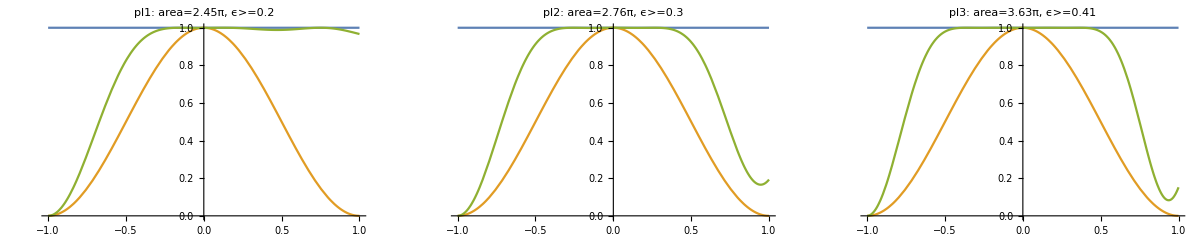

BB6 p=1/2, error=0.001

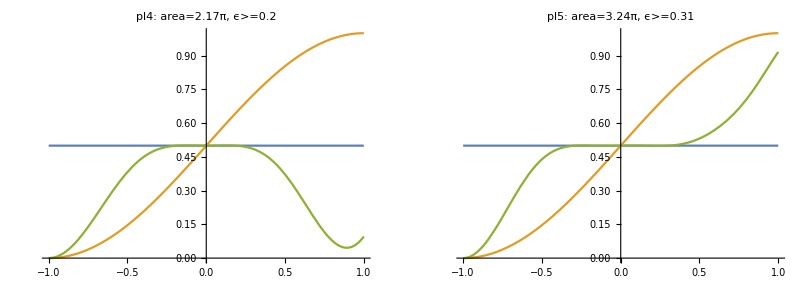

BB6 p=1/4, error=0.001

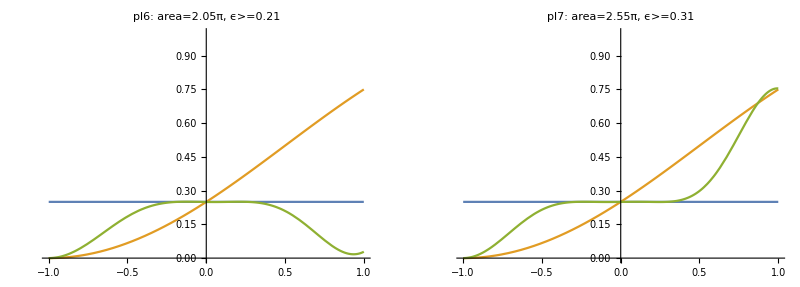

```mathematica
(*N=6 - can be optimized*)
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[-Δ3,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequence=U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label, totalArea[rule,6]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label, totalArea[rule,6]]

pl1=pltS[1,{Δ1->-0.5645,Δ2->0.5682,Δ3->0.464,Ω1->0.4091},"pl1"];
pl2=pltS[1,{Δ1->0.7016,Δ2->0.3026,Δ3->-0.1092,Ω1->0.4605},"pl2"];
pl3=pltS[1,{Δ1->0.206,Δ2->0.1043,Δ3->0.9519,Ω1->0.6058},"pl3"];

pl4=pltN[1/2,{Δ1->0.6576,Δ2->0.4893,Δ3->-0.0386,Δ4->1.8798,Δ5->0.3189,Δ6->0.0072,Ω1->0.3624},"pl4"];
pl5=pltN[1/2,{Δ1->1.1068,Δ2->0.1300,Δ3->0.5033,Δ4->-0.3553,Δ5->0.9044,Δ6->1.4934,Ω1->0.5397},"pl5"];

pl6=pltN[1/4,{Δ1->0.7042,Δ2->0.7072,Δ3->1.6157,Δ4->0.0632,Δ5->0.4087,Δ6->0.1120,Ω1->0.3412},"pl6"];
pl7=pltN[1/4,{Δ1->0.6907,Δ2->0.6637,Δ3->1.7702,Δ4->0.0169,Δ5->0.1718,Δ6->0.6926,Ω1->0.4253},"pl7"];

GGrid[Text[Style["BB6 p=1"<> error,FontSize->20]],{{pl1,pl2,pl3}},ImageSize->Full]
GGrid[Text[Style["BB6 p=1/2"<> error,FontSize->20]],{{pl4,pl5,Null}},ImageSize->Full]
GGrid[Text[Style["BB6 p=1/4"<> error,FontSize->20]],{{pl6,pl7,Null}},ImageSize->Full]
```

BB7 p=1, error=0.001

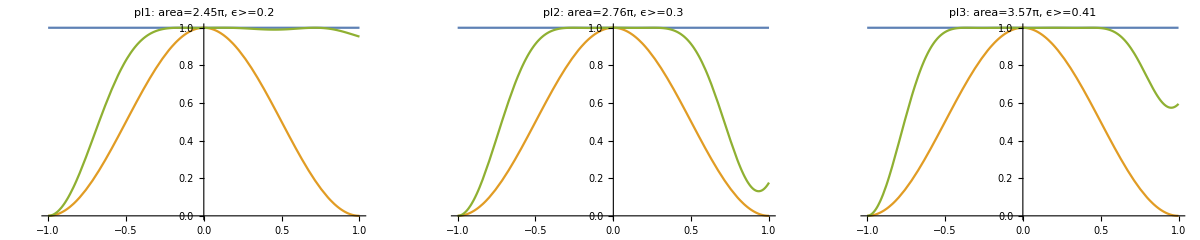

BB7 p=1/2, error=0.001

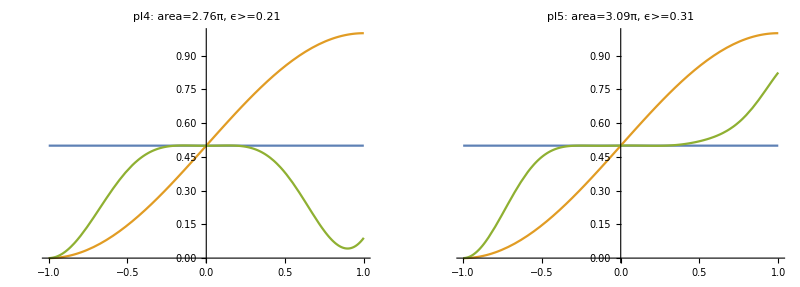

BB7 p=1/4, error=0.001

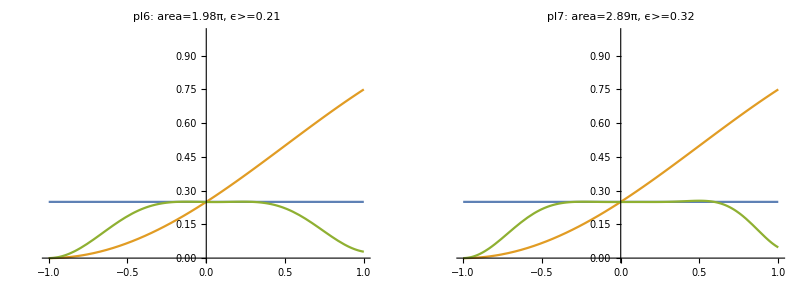

```mathematica
(*N=7*)
sequence=U[Δ7,Ω1].U[Δ6,Ω1].U[Δ5,Ω1].U[Δ4,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
sequenceS=U[-Δ1,Ω1].U[-Δ2,Ω1].U[-Δ3,Ω1].U[0,Ω1].U[Δ3,Ω1].U[Δ2,Ω1].U[Δ1,Ω1];
pltN[p_,rule_,label_]:=plot[p,err,sequence,rule,p,label,totalArea[rule,7]]
pltS[p_,rule_,label_]:=plot[p,err,sequenceS,rule,p,label,totalArea[rule,7]]

pl1=pltS[1,{Δ1->0.7908,Δ2->0.1985,Δ3->0.1177,Ω1->0.3497},"pl1"];
pl2=pltS[1,{Δ1->0.4225,Δ2->0.5247,Δ3->-0.1783,Ω1->0.3942},"pl2"];
pl3=pltS[1,{Δ1->0.9089,Δ2->0.1712,Δ3->0.1613,Ω1->0.5100},"pl3"];

pl4=pltN[1/2,{Δ1->0.7261,Δ2->0.4403,Δ3->-0.0442,Δ4->0.0404,Δ5->0.2989,Δ6->1.4926,Δ7->1.6826,Ω1->0.3950},"pl4"];
pl5=pltN[1/2,{Δ1->0.5929,Δ2->1.9610,Δ3->0.6464,Δ4->-0.216,Δ5->0.1390,Δ6->0.0202,Δ7->1.0068,Ω1->0.4409},"pl5"];

pl6=pltN[1/4,{Δ1->0.6829,Δ2->0.0341,Δ3->0.1225,Δ4->0.1621,Δ5->0.4227,Δ6->1.9472,Δ7->0.7149,Ω1->0.2832},"pl6"];
pl7=pltN[1/4,{Δ1->0.8236,Δ2->0.3754,Δ3->0.2420,Δ4->-0.0525,Δ5->0.3988,Δ6->1.0606,Δ7->1.4530,Ω1->0.4122},"pl7"];

GGrid[Text[Style["BB7 p=1"<> error,FontSize->20]],{{pl1,pl2,pl3}},ImageSize->Full]
GGrid[Text[Style["BB7 p=1/2"<> error,FontSize->20]],{{pl4,pl5,Null}},ImageSize->Full]
GGrid[Text[Style["BB7 p=1/4"<> error,FontSize->20]],{{pl6,pl7,Null}},ImageSize->Full]
```